```mathematica
(*Set as ...PathtoGithubFolder/DataFiles *)
dire="~/Dropbox/Drop_Acad/Pheno/LeoT/Github/DataFiles";
SetDirectory[dire];
Get[dire<>"/init.m"]
```

```mathematica
(*Cooling Function*)
data=Import["~/Dropbox/Drop_Acad/Pheno/LeoT/Github/DataFiles/CoolingFunc_Grackle.dat"];
coolFunc=Interpolation[Transpose[{data[[All,1]],data[[All,2]]}]];
```

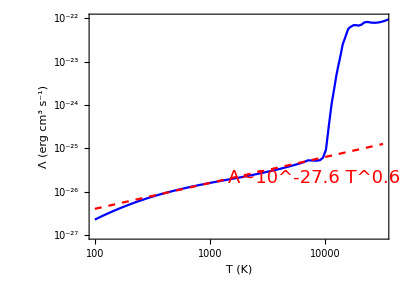

```mathematica
Show[ListLogLogPlot[{data},FrameStyle->Black,Joined->True,GridLines->Automatic,GridLinesStyle->LightGray,BaseStyle->{FontFamily->"Times",FontSize->15},Frame->True,AspectRatio->0.7,FrameLabel->{"T (K)","Λ (erg cm^3 s^-1)"},PlotStyle->{Blue},PlotRange->{{100,10^4.5},{10^-27,10^-22}}],LogLogPlot[10^-25.8(t/1000)^0.6,{t,100,10^4.5},PlotStyle->{Red,Dashed}],Graphics[{Text[Style["Λ~10^-27.6 T^0.6",Red,18],Scaled[{0.75,0.27}],{0,0},Automatic,{1,0.2}]}]]
```

```mathematica
(* Eq. D1, Terms corresponding to particle velocities and some mass factors *)
(*su:1D velocity dispersion of 1st fluid
  sv:same for 2nd fluid
  mr is the mass ratio*)
VelTerms[su_,sv_,mr_,n_]:=(2^((n+5)/2)Gamma[3+n/2] mr)/(Sqrt[Pi](mr+1)^2)(mr sv^2-su^2) (su^2+sv^2)^((n+1)/2)
```

## Leo T limits

```mathematica
(*Leo T data from Faerman et al. 2013 model*)
data=Import["~/Dropbox/Drop_Acad/Pheno/LeoT/Github/DataFiles/LeoT_profiles_Faerman13.dat"];
(*Columns are: r (kpc) n_DM (cm^-3) n_H (cm^-3) n_e (cm^-3) n_HI (cm^-3)*)
data=DeleteDuplicatesBy[data,First];
rl= data[[All,1]];
dml=Interpolation[Transpose[{data[[All,1]],mp/mgev data[[All,2]]}]];
nhl=Interpolation[Transpose[{data[[All,1]],data[[All,3]]}]];
nel=Interpolation[Transpose[{data[[All,1]],data[[All,4]]}]];
nh1l=Interpolation[Transpose[{data[[All,1]],data[[All,5]]}]];
```

InterpolatingFunction::dmval: Input value {0.0000143} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

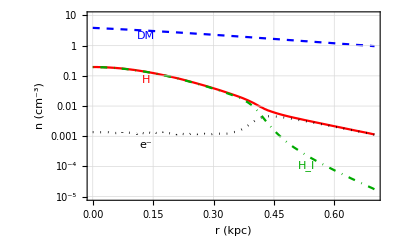

```mathematica
Show[LogPlot[{dml[r],nhl[r],nel[r],nh1l[r]},{r,0,0.7},FrameStyle->Black,GridLines->Automatic,GridLinesStyle->LightGray,BaseStyle->{FontFamily->"Times",FontSize->15},Frame->True,AspectRatio->0.6,FrameLabel->{"r (kpc)","n (cm^-3)"},PlotRange->{{0,0.7},{10^-5,10}},PlotStyle->{{Blue,Dashed},{Red},{Black,Dotted},{Darker[Green],DotDashed},{RGBColor[0.363898, 0.618501, 0.782349],Dashed},{RGBColor[0.647624, 0.37816, 0.614037],DotDashed}}(*PlotRange->{{0.002,10},{4 10^-25,10^-20}},*)],Graphics[{Text[Style["DM",Blue],Scaled[{0.2,0.87}],{0,0},Automatic,{1,0}],Text[Style["H",Red],Scaled[{0.2,0.64}],{0,0},Automatic,{1,0}],Text[Style["e^-",Black],Scaled[{0.2,0.295}],{0,0},Automatic,{1,0}],Text[Style["H_I",Darker[Green]],Scaled[{0.75,0.185}],{0,0},Automatic,{1,0}]}]]
```

```mathematica
tc=6000; (*Gas Temperature*)
```

```mathematica
coolR[r_]:= (coolFunc[tc] 10^-1.74 nhl[r]^2) (*Eq. (2)*)
```

### Dark Photon Limits

```mathematica
wp[r_]:=Sqrt[(4Pi nel[r] icm^3)/(0.0005 137) ] 10^9 ;(*ev - Plasma frequency*)
```

```mathematica
0.5 Log[4Pi tc^3 137^3(kelvin/icm)^3/10^-3 ] (*Coulomb logarithm*)
```

27.3551

```mathematica
nu[r_]:=(4 Sqrt[2 Pi] nel[r] icm^3)/(3 137^2 0.0005^0.5(tc kelvin)^1.5)  27.355 ;(*GeV - Collision frequency*)
```

```mathematica
mlist=Table[i,{i,-20.88,-11.88,1}]; (*m<wp*)
photonH[m_,r_]:=nu[r](10^m/wp[r])^2 dml[r] 1.6 10^-3 1.52 10^24
```

```mathematica
mlist2=Table[i,{i,-11.88,-5.88,1}]; (*m>wp*)
photonH2[m_,r_]:=nu[r](10^m/wp[r])^-2 dml[r] 1.6 10^-3 1.52 10^24
```

```mathematica
epsilon[m_]:=Sqrt[NIntegrate[r^2 coolR[r],{r,0,0.357}]/ NIntegrate[r^2(photonH[m,r]),{r,0,0.357}]]
epsilon2[m_]:=Sqrt[NIntegrate[r^2 coolR[r],{r,0,0.357}]/ NIntegrate[r^2(photonH2[m,r]),{r,0,0.357}]]
```

```mathematica
plot=Table[{10^mlist[[i]],epsilon[mlist[[i]]]},{i,Length[mlist]}];
plot=Join[plot,Table[{10^mlist2[[i]],epsilon2[mlist2[[i]]]},{i,Length[mlist2]}]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.137356}. NIntegrate obtained 1.63252×10^-11 and 2.65523×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

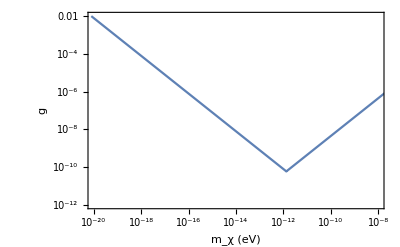

```mathematica
ListLogLogPlot[{plot},Joined->True,Frame->True,FrameStyle->Black,GridLines->Automatic,FrameLabel->{Style["m_χ (eV)",18],Style["g",18]},PlotRange->{{10^-20,10^-8},{10^-12,10^-2}}]
```

### Millicharge Limits

```mathematica
debye=Sqrt[(6000. kelvin 137)/(4Pi 2 10^-3 icm^3)] (*Debye length, GeV^-1*)
```

6.02659×10^17

```mathematica
(*Eqs. (C3) and (D1) are used here*)
```

```mathematica
crossSectionE[mx_]:= (4Pi /137^2)/(mx/(mx+.0005)me)^2(hbar cv)^2/((10^5)^4)Log[2(mx 0.0005)/(mx+0.0005) (7 Sqrt[0.938/0.0005 3])/(3 10^5)debye];
```

```mathematica
heatE[r_,mx_]:=crossSectionE[mx] me nel[r] dml[r]/mx VelTerms[ 7 Sqrt[0.938/0.0005],7,mx/0.0005,-4] 10^15
```

```mathematica
crossSectionHp[mx_]:= (4Pi /137^2)/(mx/(mx+.938) mp)^2(hbar cv)^2/((10^5)^4)Log[2 (mx 0.938)/(mx+.938) (7 Sqrt[6])/(3 10^5)debye];
```

```mathematica
heatHplus[r_,mx_]:=crossSectionHp[mx] mp nel[r] dml[r]/mx VelTerms[ 7,7. ,mx/.938,-4] 10^15
```

```mathematica
crossSectionA[mx_,ma_,z_]:=   (2Pi /137^2)/((mx ma)/(mx+ma)mgev )^2(hbar cv)^2/((10^5)^4)(Log[1+(2 (mx ma)/(mx+ma) (7Sqrt[6])/(3 10^5)0.8853/(0.0005 z^(1/3)/137))^2]-1/(1+(2 (mx ma)/(mx+ma) (7Sqrt[6])/(3 10^5)0.8853/(0.0005 z^(1/3)/137))^-2));
```

```mathematica
heatH[r_,mx_]:=crossSectionA[mx,.938,1] mp nhl[r] dml[r]/mx VelTerms[ 7,7 ,mx/(.938),-4] 10^15
```

```mathematica
heatHe[r_,mx_]:=4(*Z^2*)crossSectionA[mx,4 .938,4] 0.08 (4 mp nhl[r])dml[r]/mx VelTerms[ 7Sqrt[1/4],7 ,mx/(4 .938),-4] 10^15
```

```mathematica
mlist=Union[Table[10^i,{i,-3,-0.1,0.1}],Table[10^i,{i,-0.1,0.1,0.005}],Table[10^i,{i,0.1,1.5,0.1}]];
```

```mathematica
epsilon[mx_]:=Sqrt[NIntegrate[r^2 coolR[r],{r,0,0.357}]/Abs[NIntegrate[r^2(heatH[r,mx]+heatHe[r,mx]+heatE[r,mx]+heatHplus[r,mx]),{r,0,0.357}]]]
plot=Table[{mlist[[i]],epsilon[mlist[[i]]]},{i,Length[mlist]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.137356}. NIntegrate obtained -1.86142×10^-16 and 1.39134×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
epsilon[mx_]:=Sqrt[NIntegrate[r^2 coolR[r],{r,0,0.357}]/Abs[NIntegrate[r^2(heatE[r,mx]+heatHplus[r,mx]),{r,0,0.357}]]]
plot2=Table[{mlist[[i]],epsilon[mlist[[i]]]},{i,Length[mlist]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.137356}. NIntegrate obtained -1.86141×10^-16 and 1.39134×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
ListLogLogPlot[{plot2,plot},Joined->True,AxesLabel->{Style["m_χ (GeV)",18],Style["ϵ",20]},PlotLegends->Placed[{"e^-+H^+","+ H,He atoms"},{1,0.55}]]
```

-Graphics-

### Model indep cross section bounds (σ ∝ v^n)

#### n = -4

```mathematica
(*n=-4; H + He (assuming coulomb interaction scaling, Eq. C6) *)
leoHeat[r_,mx_,sig_]:= sig  10^15  dml[r]/mx  mp nhl[r]VelTerms[ 7.,7.,mx/0.938,-4]+ 10^15  dml[r]/mx 4 mp 0.08 nhl[r]VelTerms[ 7.Sqrt[1/4],7.,mx/(4 0.938),-4]sig (2/4(mx+4 0.938)/(mx+0.938))^2
```

```mathematica
sigbound[mx_]:=NIntegrate[r^2 coolR[r],{r,0,0.357}]/ NIntegrate[r^2 Abs[leoHeat[r,mx,1]],{r,0,0.357}]
```

```mathematica
mlist=Union[Table[10^i,{i,-3,-0.2,0.05}],Table[10^i,{i,-0.15,0.05,0.002}],Table[10^i,{i,0.1,3.5,0.1}]];
```

```mathematica
plot=Table[{mlist[[i]],sigbound[mlist[[i]]](10)^-4},{i,Length[mlist]}]; (*n=-4*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 1.9552×10^-13 and 5.78473×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

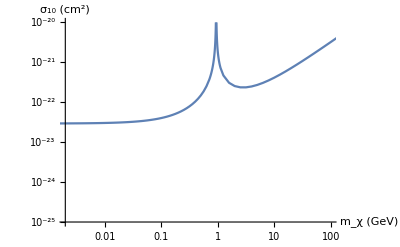

```mathematica
ListLogLogPlot[plot,PlotRange->{{0.002,100},{ 10^-25,10^-20}},Joined->True,AxesLabel->{Style["m_χ (GeV)",18],Style["σ_10 (cm^2)",18]}]
```

#### n ≠ 4

```mathematica
(* n=-2,0,2 ; H + He (assuming Born approximation scaling, Eq. C7). For e.g. n=-2 below *) 
leoHeat[r_,mx_,sig_]:= sig  10^15  dml[r]/mx  mp nhl[r]VelTerms[ 7.,7.,mx/0.938,-2] +10^15  dml[r]/mx 4 mp 0.08 nhl[r]VelTerms[ 7.Sqrt[1/4],7.,mx/(4 0.938),-2]sig 16(4(mx+0.938)/(mx+4 0.938))^2
```

```mathematica
plot=Table[{mlist[[i]],sigbound[mlist[[i]]](10)^-2},{i,Length[mlist]}]; (*n=-2*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 4.63748×10^-11 and 1.37206×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

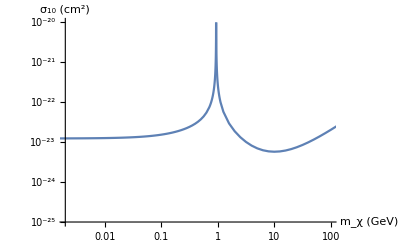

```mathematica
ListLogLogPlot[plot,PlotRange->{{0.002,100},{ 10^-25,10^-20}},Joined->True,AxesLabel->{Style["m_χ (GeV)",18],Style["σ_10 (cm^2)",18]}]
```

### DM-electron

```mathematica
heatE[r_,mx_,sig_]:=sig  10^15  dml[r]/mx me nel[r]VelTerms[ 7 Sqrt[0.938/0.0005],7.,mx/0.0005,0]
```

```mathematica
sigbound[mx_]:=NIntegrate[r^2 coolR[r],{r,0,0.357}]/ Abs[NIntegrate[r^2 heatE[r,mx,1],{r,0,0.357}]]
```

```mathematica
mlist=Union[Table[10^i,{i,-6,-0.2,0.05}],Table[10^i,{i,-0.2,0.1,0.05}],Table[10^i,{i,0.1,2,0.3}]];
```

```mathematica
plot=Table[{mlist[[i]],sigbound[mlist[[i]]]},{i,Length[mlist]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.137356}. NIntegrate obtained -0.0000148597 and 1.11071×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.121319}. NIntegrate obtained 5.75688×10^-32 and 3.35509×10^-37 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

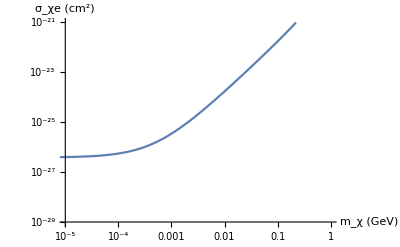

```mathematica
ListLogLogPlot[plot,PlotRange->{{10^-5,1},{10^-29,10^-21}},Joined->True,AxesLabel->{Style["m_χ (GeV)",18],Style["σ_χe  (cm^2)",18]}]
```

## Gas cloud limits

```mathematica
(*DM density of Milky Way NFW halo. Input: r(kpc), output: GeV/cm^3*)
rho0 = 0.89/(4Pi 16 NIntegrate[r/(1+r/16.)^2,{r,0,296}]);
rhoNFW[r_]:=rho0 16/ r/(1+ r/16)^2 (10^12 msun)/(mgev kpc^3)
```

```mathematica
(*Best-fit profile of MW Burkert halo*)
rhoBurkert[r_]:=4.13 10^7 msun/(mgev kpc^3)/((1+r/9.26)(1+r^2/9.26^2))
```

```mathematica
(*Halo conc. mass relation from Maccio et al. 2008*)
cvir[mvir_]:= 10^(1.051-0.099 (mvir-12))
```

```mathematica
(*Scale radius of NFW halo, in kpc*)
rsNFW[m_]:=1/cvir[m]((6.67 10^-8 1.989 10^(33+m))/(100 (70 10^(5-3))^2)1/(3.086 10^21))^(1/3)
```

```mathematica
(*Velocity dispersion of DM in km/s in the NFW halo input: [mpc, Log10[mHalo(Msun)]]*)
sigmaDM[r_,m_]:=Sqrt[0.29(1.989 10^(33+m))/(Log[1+cvir[m]]-cvir[m]/(1+cvir[m]))6.67 10^-8 Log[1+r/rsNFW[m]]/(r 3.086 10^21)(1-rsNFW[m]/r Log[1+r/rsNFW[m]])^0.41 1/10^(5 2)]
```

```mathematica
(*Reduced mass: mx=DM mass in GeV, a=Mass number*)
mu[mx_,a_]:=(mx a 0.938)/(mx+a 0.938)
```

Some clouds we explored are given below, choose one:

```mathematica
rc=Sqrt[4.68^2+1^2]; tc=400;nc=0.4; vdmc=220; vrelDMc=Sqrt[vdmc^2+3 sigmaDM[rc,12]^2];(*G33.4−8.0*)
```

```mathematica
rc=Sqrt[3.85^2+0.84^2]; tc=200;nc=2.5; vdmc=220; vrelDMc=Sqrt[vdmc^2+3 sigmaDM[rc,12]^2];(*G26.9−6.3*)
```

```mathematica
rc=Sqrt[2.34^2+0.43^2]; tc=480;nc=1.7; vdmc=220; vrelDMc=Sqrt[vdmc^2+3 sigmaDM[rc,12]^2];(*G16.0+3.0*)
```

```mathematica
rc=Sqrt[0.36^2+0.7^2]; tc=136.4;nc=0.435; vdmc=330; vrelDMc=Sqrt[vdmc^2+3 sigmaDM[rc,12]^2];(*G357.6-4.7-55*)
```

```mathematica
rc=Sqrt[0.72^2+0.48^2]; tc=366.8;nc=0.24; vdmc=330; vrelDMc=Sqrt[vdmc^2+3 sigmaDM[rc,12]^2];(*G355.3-3.3-118*)
```

```mathematica
(*Cooling time for clouds*)
3/2 kb tc/(nc coolFunc[tc])/(3.154 10^13) (*in Myr*)
```

0.718123

### Vel independent cross section limits

```mathematica
(*We use the following expressions for calculating the heating rate, Subscript[f, A] is the mass fraction*)
ToExpression["\\frac{dE}{dt dV} = \\sum_A n_A n_\\chi v_{\\textup{rel}} E_{nr} \\sigma_{A\\chi}",TeXForm,HoldForm]
ToExpression["\\sum_A \\bigg( \\frac{f_A m_p n_p}{f_p m_A}\\bigg) n_\\chi v_{\\textup{rel}} \\bigg(\\frac{\\mu_{A}^2v_{\\textup{rel}}^2}{m_A}\\bigg) \\bigg(A^2 F^2_A(E_{nr}) \\frac{\\mu_A^2}{\\mu_p^2} \\sigma_{p \\chi}\\bigg)",TeXForm,HoldForm]
```

dE/dtdV==∑_A n_A n_χ v_rel ⅇ_nr σ_(A χ)

∑_A ((f_A m_p n_p) n_χ v_rel[(μ_A^2 v_rel^2)/m_A] (A^2 F_A^2[ⅇ_nr] μ_A^2 σ_(p χ)))/((f_p m_A) μ_p^2)

```mathematica
(*Uncomment for deriving the VelTerms expression below*)
(*temp= Integrate[1/2 Sqrt[u^2+v^2-2u v c]^3,{c,-1,1},Assumptions->{v∈Reals, u∈Reals,u^2+v^2>0}];
(4Pi)/(2Pi)^(3/2)1/sv^3 Integrate[ v^2 Exp[-v^2/(2 sv^2)] temp,{v,0,Infinity},Assumptions->{v∈Reals,sv∈Reals, u∈Reals,u^2+v^2>0,u>0,sv>0}]/.{r->r1};
Simplify[%]*)
```

ⅇ^(-u^2/(2 sv^2)) √(2/π) sv (5 sv^2+u^2)+((3 sv^4)/u+6 sv^2 u+u^3) Erf[u/(√2 sv)]

```mathematica
VelTerms[u_,sv_]:=10^15(ⅇ^(-u^2/(2 sv^2)) √(2/π) sv (5 sv^2+u^2)+((3 sv^4)/u+6 sv^2 u+u^3) Erf[u/(√2 sv)] )
(*u is the DM cloud relative bulk velocity, sv is the DM velocity dispersion, both km/s*)
```

```mathematica
(*Form factor squared, Eq. C8 in paper*)
formSq[mx_,a_,v_]:=9 SphericalBesselJ[1,Sqrt[2](mu[mx,a] v/(3 10^5))5.06 Sqrt[(1.23 a^(1/3)-0.6)^2+7/3(Pi 0.52)^2-5 0.81] ]^2/(2(mu[mx,a] v/(3 10^5))^2 5.06^2((1.23 a^(1/3)-0.6)^2+7/3(Pi 0.52)^2-5 0.81) )Exp[-2(mu[mx,a] v/(3 10^5)5.06 0.9 )^2]
```

```mathematica
crossSection[mx_,a_]:=a^2 formSq[mx,a,vrelDMc] mu[mx,a]^2/mu[mx,1]^2
```

```mathematica
(*NIntegrate[(v)^2 Exp[-v^2/(2 sigmaDM[0.45,12]^2)] (-(r (-(u-v)^3 ((4+r) u+v+4 r v) Abs[u-v]+(u+v)^3 ((4+r) u-(1+4 r) v) Abs[u+v]))/(15 (1+r)^2 u v))/.{r->0.01/0.938,u->200},{v,0,500}]*)(*check for finite Subscript[v, esc]*)
```

-1.57543×10^11

```mathematica
(*Cloud heating rate in erg/cm^3/s, mx=DM mass in GeV, a=Mass number*)
cloudHeat[mx_,a_]:=(mu[mx,a]^2 mgev)/(a^2 0.938) nc  rhoNFW[rc]/mx VelTerms[vdmc,sigmaDM[rc,12]] crossSection[mx,a]
```

```mathematica
mlist=Table[10^i,{i,-3,3.9,0.05}];
```

```mathematica
plot=Table[{mlist[[i]],(nc^2 coolFunc[tc]) /(cloudHeat[mlist[[i]],1])},{i,Length[mlist]}];
plot2=Table[{mlist[[i]],(nc^2 coolFunc[tc]) /(cloudHeat[mlist[[i]],1]+0.247/0.739 cloudHeat[mlist[[i]],4])},{i,Length[mlist]}];
plot3=Table[{mlist[[i]],(nc^2 coolFunc[tc]) /(cloudHeat[mlist[[i]],1]+0.247/0.739 cloudHeat[mlist[[i]],4]+0.0063/0.739 cloudHeat[mlist[[i]],16]+0.0022/0.739 cloudHeat[mlist[[i]],12]+0.0017/0.739 cloudHeat[mlist[[i]],20]+0.0012/0.739 cloudHeat[mlist[[i]],56])},{i,Length[mlist]}];
```

```mathematica
ListLogLogPlot[{plot,plot2,plot3},Joined->True,GridLines->Automatic,PlotLegends->Placed[{"H only","+He","+O,C,Ne,Fe,Si"},{1,0.55}],AxesLabel->{"m_DM (GeV)","σ (cm^2)"}]
```

-Graphics-

### Millicharge limits

```mathematica
(*Uncomment for deriving the VelTerms expression below*)
(*temp= Integrate[1/2 Sqrt[u^2+v^2-2u v c]^-1,{c,-1,1},Assumptions->{v∈Reals, u∈Reals,u^2+v^2>0}];
(4Pi)/(2Pi)^(3/2)1/sv^3 Integrate[ v^2 Exp[-v^2/(2 sv^2)] temp,{v,0,Infinity},Assumptions->{v∈Reals,sv∈Reals, u∈Reals,u^2+v^2>0,u>0,sv>0}]/.{r->r1};
Simplify[%]*)
```

```mathematica
VelTerms[u_,sv_]:=(3 10^5)^4 10^15(1/u Erf[u/(√2 sv)]) (*in cm^3/s^3*)
```

```mathematica
(*Eq. (C5), velocities are absorbed in VelTerms2, reduced mass term gets cancelled *)
crossSection[mx_,a_]:=(2Pi)/137^2 icm^2(Log[1+(2 mu[mx,a] vrelDMc/(3 10^5)0.8853/(0.0005 a^(1/3)/137))^2]-1/(1+(2 mu[mx,a] vrelDMc/(3 10^5)0.8853/(0.0005 a^(1/3)/137))^-2));
(*Cloud heating rate in erg/cm^3/s, mx=DM mass, a=Mass number*)
atomicHeat[mx_,a_]:= mgev/(a 0.938)nc rhoNFW[rc]/mx VelTerms[220,sigmaDM[rc,12]] crossSection[mx,a]
```

```mathematica
(*For heating of electrons and ions we use Eq. (D4)*)
VelTerms2[su_,sv_,u_,mx_,ma_]:=(3 10^5)^4 10^15(-Sqrt[2/Pi]((ma+mx) su^2)/((su^2+sv^2)^(3/2))Exp[-u^2/(2 su^2+2 sv^2)]+mx/u Erf[u/Sqrt[2(su^2+sv^2)]])
```

```mathematica
crossSection2[mx_,ma_]:= (4Pi /137^2)/(mx ma/(mx+ma))^2 icm^2 Log[2 (mx ma)/(mx+ma)vrelDMc/(3 10^5)Sqrt[(tc kelvin 137)/(4Pi 0.001 nc icm^3)]]; (*0.001 just as reference*)
```

```mathematica
ionHeat[mx_,ma_]:=mgev (mx ma)/(mx+ma)^2 nc rhoNFW[rc]/mx VelTerms2[Sqrt[(tc kelvin)/ma]3 10^5,sigmaDM[rc,12],220,mx,ma]crossSection2[mx,ma]
```

```mathematica
mlist=Table[10^i,{i,-2.7,1,0.05}];
```

```mathematica
(*H-atom + He-atom + Electrons + Carbon-ion + Iron-ion*)
plot=Table[{mlist[[i]],Sqrt[nc^2 coolFunc[tc] /(atomicHeat[mlist[[i]],1]+0.247/0.739 1/4 atomicHeat[mlist[[i]],4]+(0.0022/0.739 1/12+0.0012/0.739 1/56)ionHeat[mlist[[i]],0.0005]+0.0022/0.739 1/12 ionHeat[mlist[[i]],12 0.938]+0.0012/0.739 1/56 ionHeat[mlist[[i]],56 0.938])]},{i,Length[mlist]}];
```

```mathematica
plot2=Table[{mlist[[i]],Sqrt[nc^2 coolFunc[tc] /((0.0022/0.739 1/12+0.0012/0.739 1/56)ionHeat[mlist[[i]],0.0005]+0.0022/0.739 1/12 ionHeat[mlist[[i]],12 0.938]+0.0012/0.739 1/56 ionHeat[mlist[[i]],56 0.938])]},{i,Length[mlist]}];
plot3=Table[{mlist[[i]],Sqrt[nc^2 coolFunc[tc] /((0.0022/0.739 1/12+0.0012/0.739 1/56)ionHeat[mlist[[i]],0.0005])]},{i,Length[mlist]}];
```

```mathematica
ListLogLogPlot[{plot3,plot2,plot},PlotStyle->{,Dashed,},Joined->True,AxesLabel->{"m_DM (GeV)","ϵ"},GridLines->Automatic,PlotLegends->Placed[{"e^-","+C^+,Fe^+","+Neutral H,He"},{1,0.55}]]
```

-Graphics-